data from before the MOT tubes were installed on the macor bridge. this gives the beam waists viewing the beam head on, but i’m just using the profiles for a thesis figure.

```mathematica
img=ImageData[ColorConvert[-Graphics-,"Grayscale"]];
{dimx,dimy}=Dimensions[img]
```

{1059,1106}

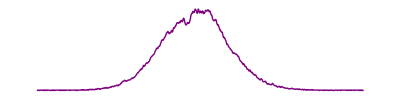

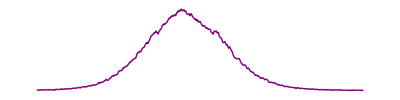

```mathematica
ListPlot[img[[Floor[dimx/2],;;-3]],Axes->False,Joined->True,AspectRatio->1/4,PlotStyle->{Purple,Thick}]
ListPlot[img[[;;-2,dimy/2]],Axes->False,Joined->True,AspectRatio->1/4,PlotStyle->{Purple,Thick}]
```

```mathematica
img=ImageData[ColorConvert[-Graphics-,"Grayscale"]];
{dimx,dimy}=Dimensions[img]
```

{971,1007}

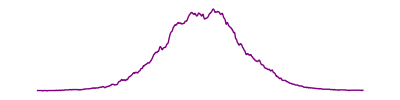

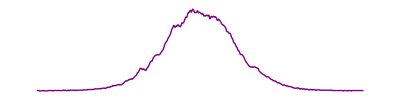

```mathematica
ListPlot[img[[Floor[dimx/2],;;-3]],Axes->False,Joined->True,AspectRatio->1/4,PlotStyle->{Purple,Thick}]
ListPlot[img[[;;-2,Floor[dimy/2]]],Axes->False,Joined->True,AspectRatio->1/4,PlotStyle->{Purple,Thick}]
```